Un octave en musique est défini comme l’intervalle entre deux notes qui correspond à un dédoublement de la fréquance:

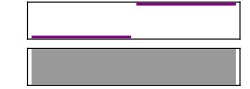

```mathematica
Sound[{SoundNote[0],SoundNote[12]}]
```

Traditionnellement, on divise un octave en 12 notes : Do, Do#/Ré♭, Ré, Ré#/Mi♭, Mi, Fa, Fa#/Sol♭, Sol, Sol#/La♭, La, La#/Si♭ et Si. Après un octave, on recommence au Do. Ainsi, on peut assimiler les notes du piano à ℤ/12ℤ.

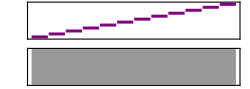
-Graphics-
{0,1,2,3,4,5,6,7,8,9,10,11}

```mathematica
Column[
{
Sound[Table[SoundNote[n,0.25],{n,0,11}]],
Range[0,11]}
]
```

En faisant correspondre l’addition de n à un intervalle de n semitons, on voit que les notes sont un exemple du groupe cyclique d’ordre 12, noté C_12.
On peut ainsi composer deux intervalles pour en obtenir un nouveau, et on obtient le tableau suivant :

```mathematica
TableForm[GroupMultiplicationTable[CyclicGroup[12]] -1,TableHeadings->{Range[0,11],Range[0,11]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0
2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1
3 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2
4 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3
5 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4
6 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5
7 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6
8 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
9 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
10 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
11 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

On peut également essayer de composer un intervalle avec lui même un certain nombre de fois, et regarder les intervalles obtenus.

```mathematica
Manipulate[
Column[
{
Sound[
{Table[SoundNote[Mod[k n,12],0.25],{k,0,11}]}
],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

On remarque qu’on obtient tous les intervalles que pour 3 valeurs de n : il s’agit de 1, 5, 7 et 11. ON appelle mathématiquement ces valeurs les générateurs du groupe (ℤ/12ℤ,+). Les éléments du groupe sont dans un ordre bien déterminé, et ces dispositions sont nommés en théorie de la musique. Pour n=1, il s’agit de la gamme chromatique, pour n = 5, il s’agit du cercle des quartes, pour n = 7, on parle du cercles des quintes et enfin pour n = 11 il s’agit de la gamme chromatique inversée.
Les cercles des quintes et des quartes sont souvent utilisées en musique, car ils sonnent particulièrement bien, e.g. Take me to the moon:

We can notice that these values correspond to the only n ∈ [0,11] with GCD[n,12] = 1.

```mathematica
Manipulate[
Column[
{
StringJoin["PGCD(",ToString[n],",12) = ",ToString[GCD[12,n]]],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

We see in general that the number of elements generated by n is equal to 12/(GCD(12,n)).

```mathematica
Manipulate[
Column[
{
StringJoin["12 / PGCD(",ToString[n],",12) = ",ToString[12/GCD[12,n]]],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
"`"
```

```mathematica
Sound[{SoundNote[0],SoundNote[0.5,1,"Square"],SoundNote[1]}]
```

Sound[{SoundNote[0],SoundNote[0.5],SoundNote[1]}]

```mathematica
Solve[{440==b^(9+c),220==b^(-3+c)},{b,c}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{b→ⅇ^(1/12 (-Log[220]+Log[440])),c→(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])}}

```mathematica
{b,c}={ⅇ^(1/12 (-Log[220]+Log[440])),(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])}
```

{ⅇ^(1/12 (-Log[220]+Log[440])),(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])}

```mathematica
frequency[x_]:=b^(x+c)
```

```mathematica
frequency[(12 0.5)/24]
```

frequency[0.25]

```mathematica
Sin[2π t*265.43099677611224]
```

Sin[1667.75 t]

```mathematica
Play[Sin[1667.7521390137006 t],{t,0,0.5}]
```

-Graphics-

```mathematica
Manipulate[
Sound[
Table[
Play[Sin[2π t*frequency[12.0*n/m]],{t,0,0.5}],
{n,0,m-1}
]
],
{{m,12},2,50,1}
]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[Sound[Table[Play[Sin[2 Pi t*frequency[12.0*n/m]],{t,0,0.5}],{n,0,m-1}]],{{m,12},2,50,1}]
```

```mathematica
(*Calculate b and c numerically*){b,c}=N@{E^((-Log[220]+Log[440])/12),(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])};

(*Define frequency function*)
frequency[x_?NumericQ]:=b^(x+c)
Manipulate[
Module[
{tones},
tones=Table[
With[
{k=n},
Play[
Sin[2 Pi t*frequency[12.0*k/m]],
{t,0,0.5},
SampleRate->8000
]
],
{n,0,m-1}
];
Sound[tones]
(*a list of Sound objects plays in sequence*)
],
{{m,12},2,50,1}
]
```

Sound::ssnm: A good PlayRange could not be found since most of the samples are not evaluating to machine-sized real numbers.

General::stop: Further output of Sound::ssnm will be suppressed during this calculation.

```mathematica
(*Calculate b and c numerically*){b,c}=N@{E^((-Log[220]+Log[440])/12),(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])};

(*Define frequency function*)
frequency[x_?NumericQ]:=b^(x+c)
Manipulate[
Column[{
Module[
{tones},
tones=Table[
With[
{k=n},
Play[
Sin[2 Pi t*frequency[12.0*Mod[l k,m]/m]],
{t,0,0.5},
SampleRate->8000
]
],
{n,0,m-1}
];
Sound[tones]
(*a list of Sound objects plays in sequence*)
],
ToString[m]<>" / GCD("<>ToString[l],", "<>ToString[m]<>") = "<>ToString[m/GCD[m,l]],
UniqueElements[{Table[Mod[k l,m],{k,0,m-1}]}][[1]],
"ϕ["<>ToString[m]<>"] = "<>ToString[EulerPhi[m]]
}],
{{m,12},2,30,1},
{{l,1},0,m,1}
]
```